# Gravitational Wave Astrometry

We will illustrate the effect of of GWs on a field of stars. See Mihaylov et al (2018) for a derivation of the astrometric effect of a GW (https://link.aps.org/doi/10.1103/PhysRevD.97.124058).

First, define the 3D effective displacement from an arbitrary plane-GW h_ij coming from a direction q_i and affecting a star at location n_i on the celestial sphere (Eq. 20 in the paper cited above):

#### Gravitational waves

```mathematica
dN[h_,n_,q_]:=1/2 Table[(n[[i]]-q[[i]])/(1-Dot[q,n])Sum[h[[j,k]]n[[j]]n[[k]],{j,1,3},{k,1,3}] - Sum[h[[i,j]]n[[j]],
{j,1,3}],{i,1,3}]
```

Assuming GR, the strain can be decomposed into the usual plus and cross polarization tensors:

```mathematica
ep=({{1, 0, 0}, {0, -1, 0}, {0, 0, 0}});
ec=({{0, 1, 0}, {1, 0, 0}, {0, 0, 0}});
```

WARNING: this assumes the GW propagates in the z direction! We can generalize it later, but for now this means that we must have q=(0,0,1) below.

We will further assume a continuous wave of certain instantaneous phase ϕ and amplitude A:

```mathematica
H[Ap_,Ac_,ϕ_]:=Ap Cos[ϕ]ep+Ac Cos[ϕ]ec
```

#### Star field

Now all we need is a field of stars to displace. We will place the stars randomly over the sphere (NOTE: we could do something nicer, like Fibonacci like grid). We can do this by drawing Cartesian coordinates from a 3D unit Gaussian, and then normalizing each entry:

```mathematica
Nstars = 1000;
stars=Map[Normalize,RandomVariate[NormalDistribution[],{Nstars,3}]];
```

For visualization purposes, we will only want stars in a single hemisphere, so let’s force that all stars have a positive z component (folding stars from one hemisphere into the other)

```mathematica
hemisphericstars=Map[If[#[[3]]<0,-#,#]&,stars];
```

```mathematica
ListPointPlot3D[{stars,hemisphericstars},PlotStyle->{Red,Blue},PlotLegends->{"initial stars","adjusted stars"}, BoxRatios->{1,1,1}]
```

-Graphics3D-

Finally, we will want to look at the projection of the hemisphere:

```mathematica
flatstars = Map[#[[1;;2]]&,hemisphericstars];
```

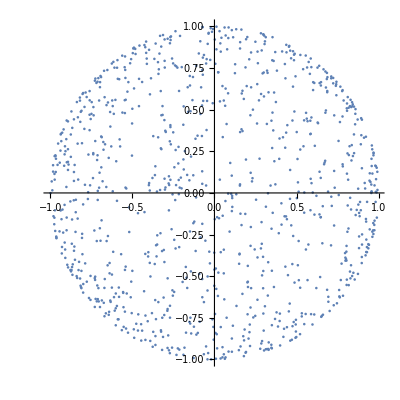

```mathematica
ListPlot[flatstars,AspectRatio->1]
```

#### Displacement

We can now apply the GW to displace our stars.

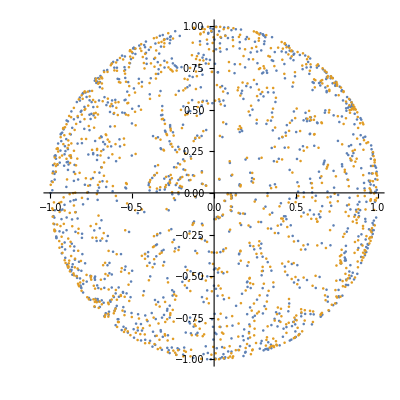

```mathematica
dStar[n_]:=dN[H[0,0.1,0],n, {0,0,1}]

newstars = Map[Normalize,hemisphericstars + Map[dStar,hemisphericstars]];
newflatstars = Map[#[[1;;2]]&,newstars];

diffvecs=Transpose[{flatstars,newflatstars-flatstars}];

ListPlot[{flatstars,newflatstars},AspectRatio->1]
```

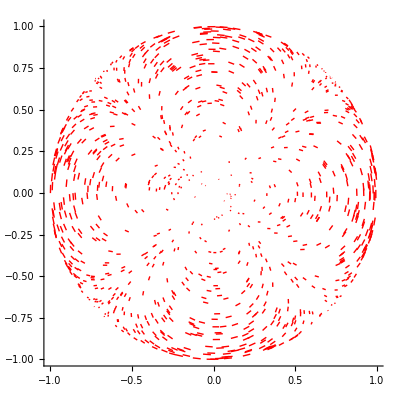

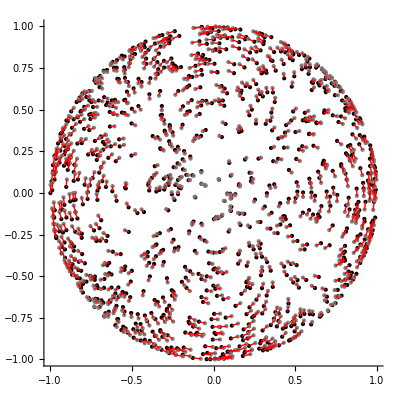

```mathematica
vectors=MapThread[Line[{#1,#2}]&,{flatstars,newflatstars}];Graphics[{Red,vectors},Axes->True]
pointGraphics=Graphics[{Black,PointSize[Small],Point[flatstars],Gray,Point[newflatstars]}];
Show[pointGraphics,Graphics[{Red,vectors}],Axes->True]
```

#### Animate

We can animate the above plot.

```mathematica
PlotStars[Ap_,Ac_,ϕ_]:=Module[{dStar, newstars,newflatstars},
(*Define the dStar function*)
dStar[n_]:=dN[H[Ap,Ac,ϕ],n,{0,0,1}];

(*Assuming hemisphericstars and flatstars are defined earlier or are global*)
newstars=Map[Normalize,hemisphericstars+Map[dStar,hemisphericstars]];
newflatstars=Map[#[[1;;2]]&,newstars];

(*Return the ListPlot*)
ListPlot[{flatstars,newflatstars},PlotStyle->{Gray,Blue},AspectRatio->1]
];
```

```mathematica
Animate[PlotStars[0.1,0,ϕ],{ϕ,0,2π}]
```

```mathematica
PlotDisplacements[Ap_,Ac_,ϕ_]:=Module[{dStar, newstars,newflatstars,vectors},
(*Define the dStar function*)
dStar[n_]:=dN[H[Ap,Ac,ϕ],n,{0,0,1}];

(*Assuming hemisphericstars and flatstars are defined earlier or are global*)
newstars=Map[Normalize,hemisphericstars+Map[dStar,hemisphericstars]];
newflatstars=Map[#[[1;;2]]&,newstars];

(*Return the plot*)
vectors=MapThread[Line[{#1,#2}]&,{flatstars,newflatstars}];Graphics[{Red,vectors},Axes->True]
];
```

```mathematica
animation=Animate[PlotDisplacements[0.1,0,ϕ],{ϕ,0,2π}]
```

```mathematica
relativePath=FileNameJoin[{NotebookDirectory[],"plus_displacement.gif"}];
Export[relativePath,animation]
```

/Users/misi/Simons Foundation Dropbox/Max Isi/getty/plus_displacement.gif

```mathematica
PlotBoth[Ap_,Ac_,ϕ_]:=Module[{dStar, newstars,newflatstars,vectors,pointGraphics},
(*Define the dStar function*)
dStar[n_]:=dN[H[Ap,Ac,ϕ],n,{0,0,1}];

(*Assuming hemisphericstars and flatstars are defined earlier or are global*)
newstars=Map[Normalize,hemisphericstars+Map[dStar,hemisphericstars]];
newflatstars=Map[#[[1;;2]]&,newstars];

(*Return the plot*)
vectors=MapThread[Line[{#1,#2}]&,{flatstars,newflatstars}];pointGraphics=Graphics[{Gray,PointSize[Small],Point[flatstars],Black,Point[newflatstars]}];
Show[pointGraphics,Graphics[{Red,vectors}],Axes->True]
];
```

```mathematica
Animate[PlotBoth[0.1,0,ϕ],{ϕ,0,2π}]
```